```mathematica
eq=h+u^2*h/2+r*u-u^3/2
```

h+r u+(h u^2)/2-u^3/2

```mathematica
deq=D[eq,u]
```

r+h u-(3 u^2)/2

```mathematica
sol=Solve[deq==0,u]
```

{{u→1/3 (h-√(h^2+6 r))},{u→1/3 (h+√(h^2+6 r))}}

```mathematica
umin=sol[[1,1,2]]
umax=sol[[2,1,2]]
```

1/3 (h-√(h^2+6 r))

1/3 (h+√(h^2+6 r))

```mathematica
eqhcmin=eq/.u->umin;
```

```mathematica
solmin=Solve[eqhcmin==0,r][[1,1,2]];
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

```mathematica
solsimp=solmin/.h^b_ /; b>4 ->0;
solsimp=solsimp/.Sqrt[h^4]->h^2;
solsimp = solsimp/.h^b_ /; b>=4 ->0
```

-h^2/24+3/2 (h^2)^(1/3)+1/2 (h^2)^(2/3)

```mathematica
SetDirectory[NotebookDirectory[]];
<<MaTeX`
```

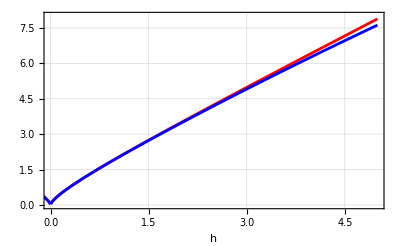

bifurcation_curves.pdf

```mathematica
PBstyle = {PlotStyle->{{Thickness[0.005],Red}, {Thickness[0.005], Blue}},Frame->True, FrameStyle->Directive[Black, Thickness[0.003],  9, FontFamily->"Euclid"], GridLines->Automatic,ImagePadding->{{30,2},{37,4}}, AxesLabel->Automatic  };
xticks={0,5};
yticks={0,8};
xlabel="h";
ylabel="r(h)";
origin={-100,-100};
fig=Plot[{solmin,solsimp},{h,-5,5}, Evaluate@PBstyle,PlotRange->{{Min[xticks], Max[xticks]}, {Min[yticks], Max[yticks]}}, AxesOrigin->origin, FrameLabel->{MaTeX[xlabel], MaTeX[ylabel]}, ImageSize->{{210}}]
Export["bifurcation_curves.pdf", fig, ImageResolution->1000,ImagePadding->None]
```